Definicje funkcji używanych przy mapowaniu:

```mathematica
GetMax[x_] :={First[x], Max[Take[x,{2,Length[x]}]]};
GetMean[x_] :={First[x], Mean[Take[x,{2,Length[x]}]]};
GetVariance[x_] :={First[x], Variance[Take[x,{2,Length[x]}]]};
GetPlusStandardDeviation[x_] :={First[x],Mean[Take[x,{2,Length[x]}]] + StandardDeviation[Take[x,{2,Length[x]}]]};
GetMinusStandardDeviation[x_] :={First[x],Mean[Take[x,{2,Length[x]}]] - StandardDeviation[Take[x,{2,Length[x]}]]};
```

```mathematica
UNI :="uniform"; MIN := "minimum"; AGL := "always_go_left";
Strategies := {UNI, MIN, AGL};
CCP := "coupon_collector"; BPP := "birthday_paradox"; MLP := "max_load";
Problems := {CCP, BPP, MLP};
RawResults[s_,p_,d_] := ReadList[StringJoin["/home/dev/Workspaces/Studies/AnalAlgo/BallsAndCups/cups_" ,s,"_",p,"_",ToString[d],".m"], Number, RecordLists->True];
ResultsMax[s_,p_,d_] := Map[GetMax, RawResults[s,p,d]];
ResultsMean[s_,p_,d_] := Map[GetMean,  RawResults[s,p,d]];
ResultsVariance[s_,p_,d_] := Map[GetVariance,  RawResults[s,p,d]];
ResultsPlusStandardDeviation[s_,p_,d_] := Map[GetPlusStandardDeviation,  RawResults[s,p,d]];
ResultsMinusStandardDeviation[s_,p_,d_] := Map[GetMinusStandardDeviation,  RawResults[s,p,d]];
```

Wyświetlanie wyników dla Coupon Collector Problem z użyciem rozkładu jednostajnego:

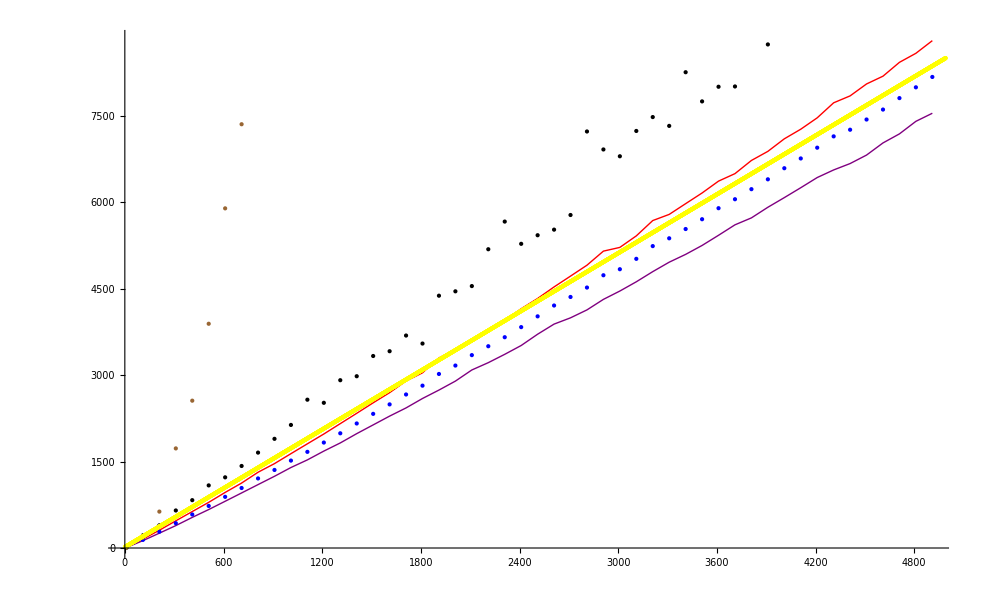

```mathematica
Show[
ListLinePlot[ResultsPlusStandardDeviation[MIN,CCP,10],PlotStyle->Red],
ListLinePlot[ResultsMinusStandardDeviation[MIN,CCP,10],PlotStyle->Purple],
ListPlot[ResultsMax[MIN,CCP,10],PlotStyle -> Black],
ListPlot[ResultsMean[MIN,CCP,10],PlotStyle -> Blue],
ListPlot[ResultsVariance[MIN,CCP,10], PlotStyle->Brown],
ListPlot[Table[1.7n,{n, 10, 5000}], PlotStyle-> Yellow]
]
```

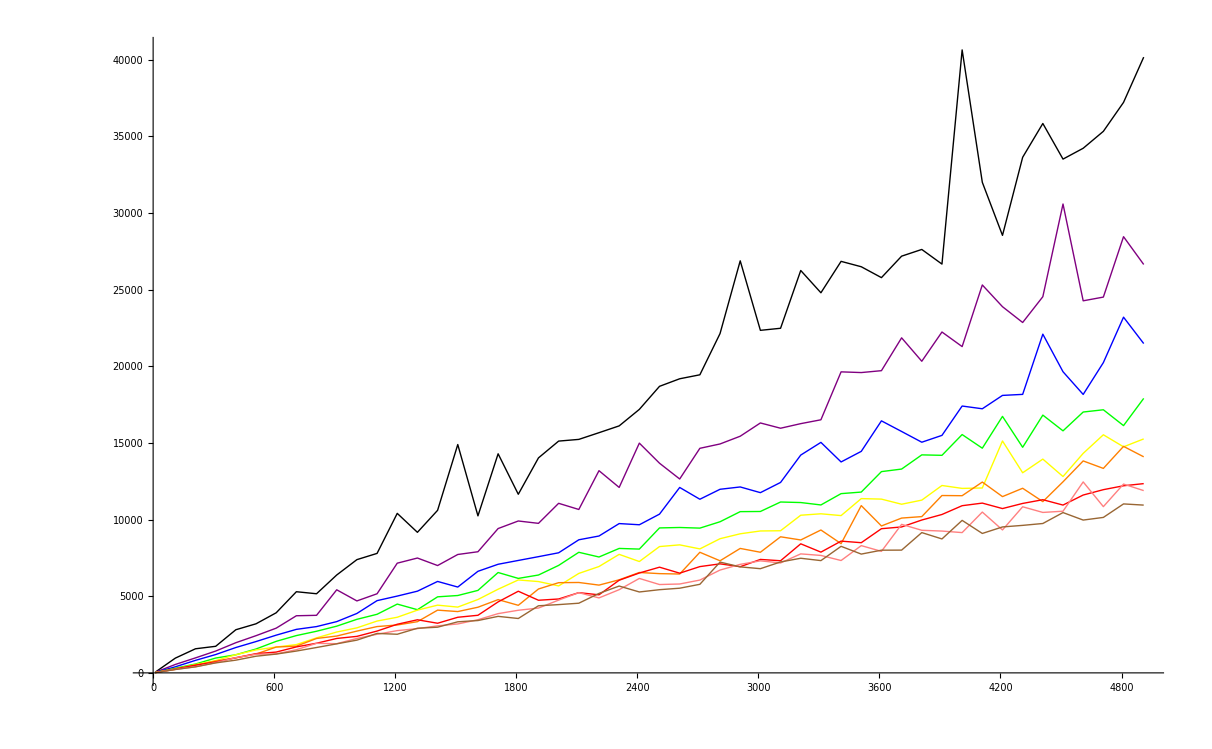

```mathematica
Show[
ListLinePlot[ResultsMax[MIN,CCP,2],PlotStyle -> Black],
ListLinePlot[ResultsMax[MIN,CCP,3],PlotStyle -> Purple],
ListLinePlot[ResultsMax[MIN,CCP,4],PlotStyle -> Blue],
ListLinePlot[ResultsMax[MIN,CCP,5],PlotStyle -> Green],
ListLinePlot[ResultsMax[MIN,CCP,6],PlotStyle -> Yellow],
ListLinePlot[ResultsMax[MIN,CCP,7],PlotStyle -> Orange],
ListLinePlot[ResultsMax[MIN,CCP,8],PlotStyle -> Red],
ListLinePlot[ResultsMax[MIN,CCP,9],PlotStyle -> Pink],
ListLinePlot[ResultsMax[MIN,CCP,10],PlotStyle -> Brown]
]
```

Wyświetlanie wyników dla Birthday Paradox Problem z użyciem rozkładu jednostajnego:

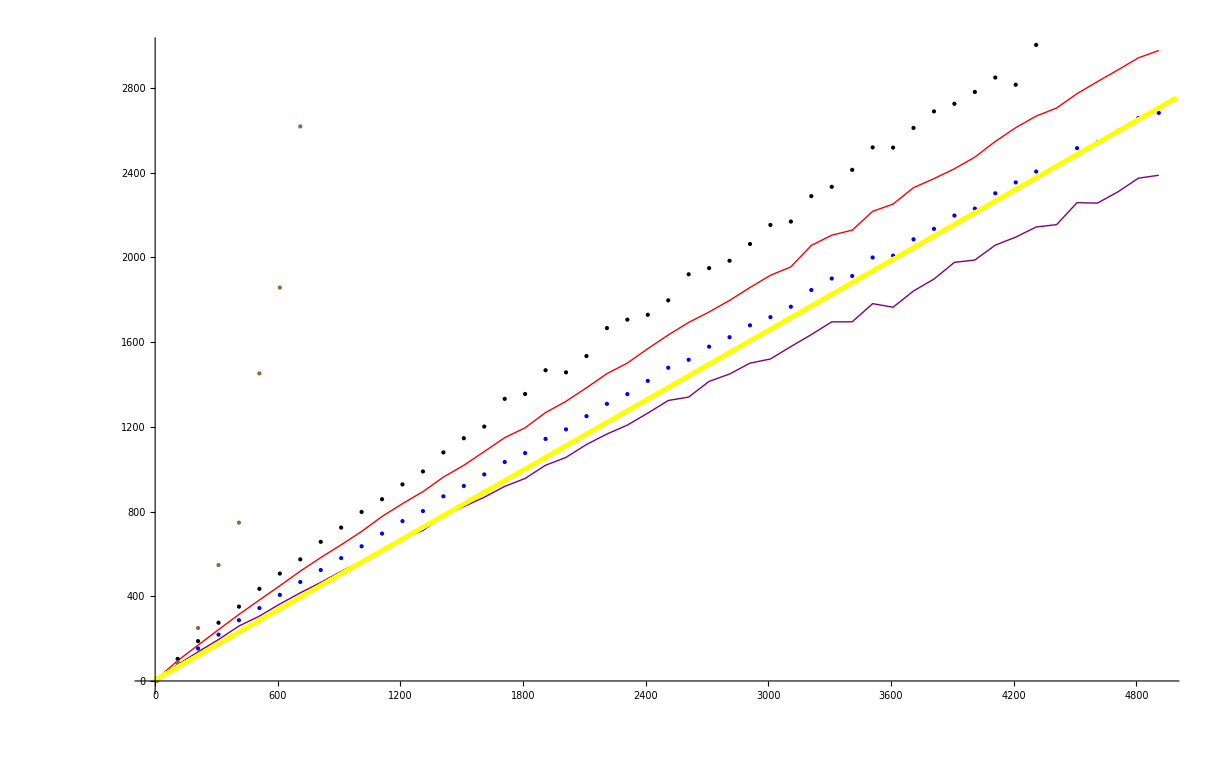

```mathematica
Show[
ListLinePlot[ResultsPlusStandardDeviation[MIN,BPP,10],PlotStyle->Red],
ListLinePlot[ResultsMinusStandardDeviation[MIN,BPP,10],PlotStyle->Purple],
ListPlot[ResultsMax[MIN,BPP,10],PlotStyle -> Black],
ListPlot[ResultsMean[MIN,BPP,10],PlotStyle -> Blue],
ListPlot[ResultsVariance[MIN,BPP,10], PlotStyle->Brown],
ListPlot[Table[0.55n,{n, 10, 5000}], PlotStyle-> Yellow]
]
```

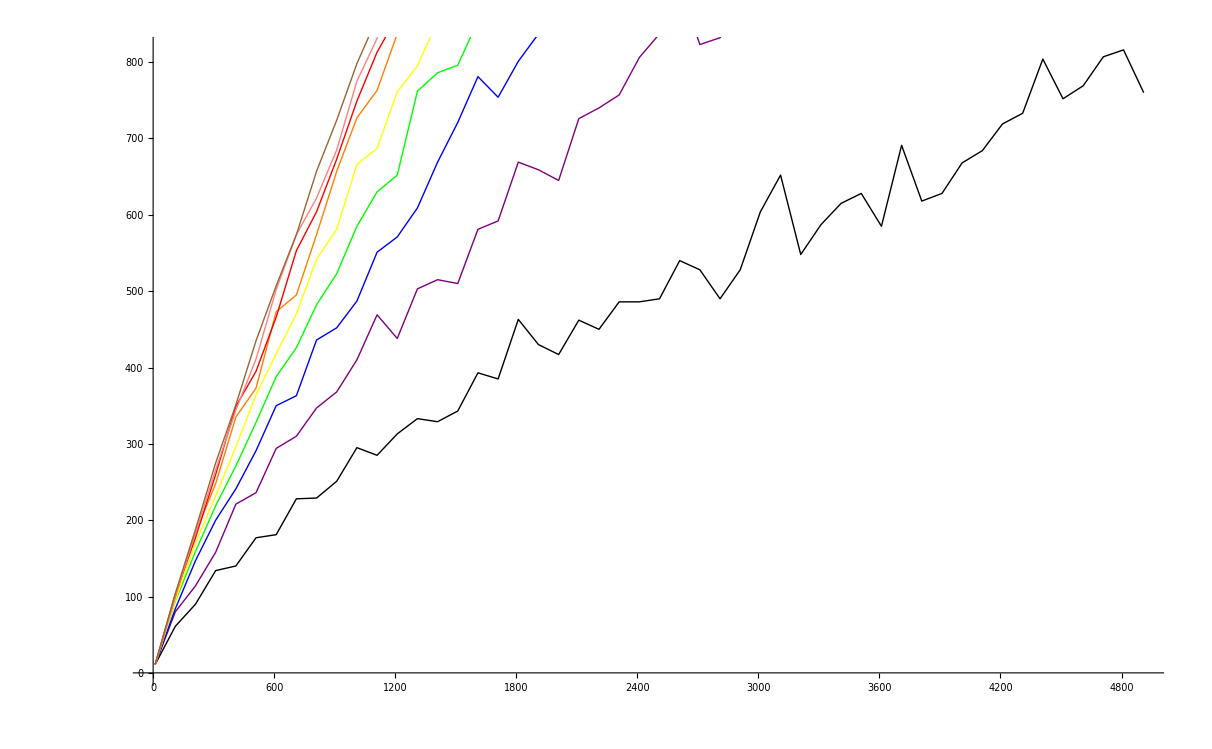

```mathematica
Show[
ListLinePlot[ResultsMax[MIN,BPP,2],PlotStyle -> Black],
ListLinePlot[ResultsMax[MIN,BPP,3],PlotStyle -> Purple],
ListLinePlot[ResultsMax[MIN,BPP,4],PlotStyle -> Blue],
ListLinePlot[ResultsMax[MIN,BPP,5],PlotStyle -> Green],
ListLinePlot[ResultsMax[MIN,BPP,6],PlotStyle -> Yellow],
ListLinePlot[ResultsMax[MIN,BPP,7],PlotStyle -> Orange],
ListLinePlot[ResultsMax[MIN,BPP,8],PlotStyle -> Red],
ListLinePlot[ResultsMax[MIN,BPP,9],PlotStyle -> Pink],
ListLinePlot[ResultsMax[MIN,BPP,10],PlotStyle -> Brown]
]
```

Wyświetlanie wyników dla Max Load Problem z użyciem rozkładu jednostajnego:

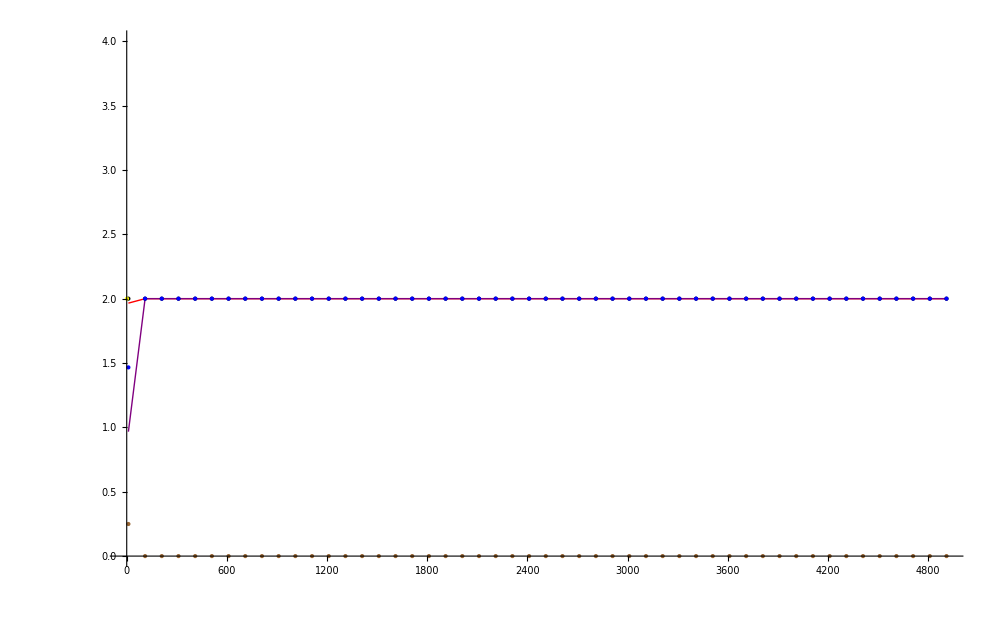

```mathematica
Show[
ListLinePlot[ResultsPlusStandardDeviation[MIN,MLP,10],PlotStyle->Red],
ListLinePlot[ResultsMinusStandardDeviation[MIN,MLP,10],PlotStyle->Purple],
ListPlot[ResultsMax[MIN,MLP,10],PlotStyle -> Black],
ListPlot[ResultsMean[MIN,MLP,10],PlotStyle -> Blue],
ListPlot[ResultsVariance[MIN,MLP,10], PlotStyle->Brown],
ListPlot[Table[2,{n,0,100, 5000}], PlotStyle-> Yellow]
]
```

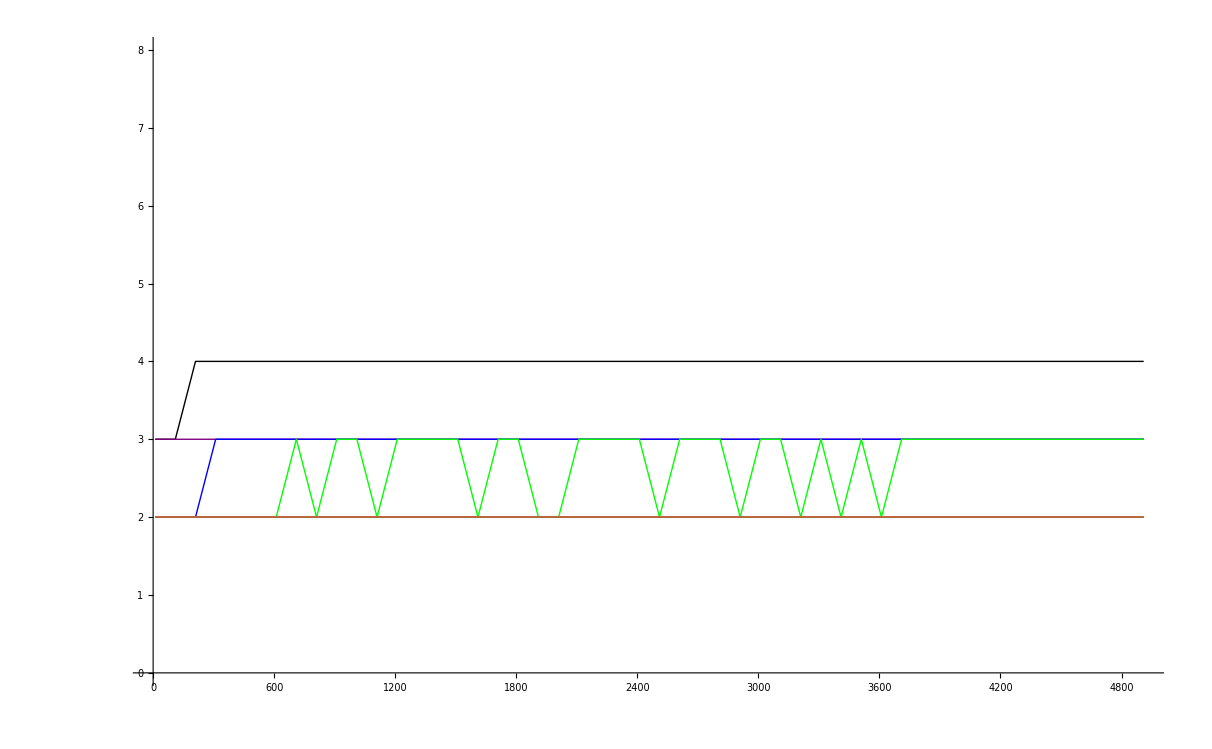

```mathematica
Show[
ListLinePlot[ResultsMax[MIN,MLP,2],PlotStyle -> Black],
ListLinePlot[ResultsMax[MIN,MLP,3],PlotStyle -> Purple],
ListLinePlot[ResultsMax[MIN,MLP,4],PlotStyle -> Blue],
ListLinePlot[ResultsMax[MIN,MLP,5],PlotStyle -> Green],
ListLinePlot[ResultsMax[MIN,MLP,6],PlotStyle -> Yellow],
ListLinePlot[ResultsMax[MIN,MLP,7],PlotStyle -> Orange],
ListLinePlot[ResultsMax[MIN,MLP,8],PlotStyle -> Red],
ListLinePlot[ResultsMax[MIN,MLP,9],PlotStyle -> Pink],
ListLinePlot[ResultsMax[MIN,MLP,10],PlotStyle -> Brown]
]
```